# Zero Temperature Physics of the Full Singlet Model

Isaac R. Wang

This code analyze the zero temperature physics of the naturally light singlet scalar model. The interacting potential is chosen to be of the full form. That means the light scalar is regarded as the angular direction of the scalar in the UV theory.

```mathematica
Quit[];
```

```mathematica
$Assumptions={{μH,λ,μS,A,x1,x2,x3,h,v,w,mS,mh,θ,f,f-S,μHsq,μSsq}∈PositiveReals,{S,α,β}∈Reals,-π<=α<=π,-π<=β<=π};
MakeBoxes[μSsq,TraditionalForm]:="μ_S^2";
MakeBoxes[μHsq,TraditionalForm]:="μ_H^2";
MakeBoxes[x1,TraditionalForm]:="x_1";
MakeBoxes[x2,TraditionalForm]:="x_2";
MakeBoxes[x3,TraditionalForm]:="x_3";
MakeBoxes[mh,TraditionalForm]:="m_h";
MakeBoxes[mS,TraditionalForm]:="m_S";
```

## Potential

```mathematica
V0=-μHsq(H†.H)+λ (H†.H)^2+μSsq f^2(1-Cos[S/f+α])-A f( (H†.H)-v^2)Sin[S/f+β];
dof={H->1/(√2){x1+ⅈ x2,h+ⅈ x3}};
truevev={x1->0,x2->0,x3->0};
physical‵vev={h->√2 v,S->0};
Vtree=V0/.dof//Simplify
Vtree‵nogs=Vtree/.truevev//Simplify
```

1/4 (-2 A f sin(β+S/f) (h^2+x_1^2+x_2^2+x_3^2-2 v^2)-4 f^2 μ_S^2 (cos(α+S/f)-1)+λ (h^2+x_1^2+x_2^2+x_3^2)^2-2 μ_H^2 (h^2+x_1^2+x_2^2+x_3^2))

1/4 (-2 A f (h^2-2 v^2) sin(β+S/f)-4 f^2 μ_S^2 (cos(α+S/f)-1)+h^4 λ-2 h^2 μ_H^2)

## Tree-level physics

### Mass spectrum

```mathematica
mass‵matrix=D[Vtree,{{x1,x2,x3,h,S},2}]/.truevev//Simplify;
mass‵matrix//MatrixForm
```

(-A f sin(β+S/f)+h^2 λ-μ_H^2 | 0 | 0 | 0 | 0
0 | -A f sin(β+S/f)+h^2 λ-μ_H^2 | 0 | 0 | 0
0 | 0 | -A f sin(β+S/f)+h^2 λ-μ_H^2 | 0 | 0
0 | 0 | 0 | -A f sin(β+S/f)+3 h^2 λ-μ_H^2 | -A h cos(β+S/f)
0 | 0 | 0 | -A h cos(β+S/f) | (A (h^2-2 v^2) sin(β+S/f))/(2 f)+μ_S^2 cos(α+S/f))

```mathematica
mStree=Eigenvalues[mass‵matrix[[4;;5,4;;5]]][[1]]//Simplify
mhtree=Eigenvalues[mass‵matrix[[4;;5,4;;5]]][[2]]//Simplify
mgs=mass‵matrix[[1,1]]
```

-1/(4 f)(√((A (2 f^2-h^2+2 v^2) sin(β+S/f)+2 f (μ_H^2-3 h^2 λ)-2 f μ_S^2 cos(α+S/f))^2+4 f (A (A f (h^2+2 v^2) cos(2 (β+S/f))+3 A f h^2-2 A f v^2+2 f^2 μ_S^2 sin(α+β+(2 S)/f)-2 f^2 μ_S^2 sin(α-β)-6 h^4 λ sin(β+S/f)+2 h^2 μ_H^2 sin(β+S/f)+12 h^2 λ v^2 sin(β+S/f)-4 μ_H^2 v^2 sin(β+S/f))-4 f μ_S^2 (3 h^2 λ-μ_H^2) cos(α+S/f)))+2 A f^2 sin(β+S/f)-A h^2 sin(β+S/f)+2 A v^2 sin(β+S/f)-6 f h^2 λ-2 f μ_S^2 cos(α+S/f)+2 f μ_H^2)

1/(4 f)(√((A (2 f^2-h^2+2 v^2) sin(β+S/f)+2 f (μ_H^2-3 h^2 λ)-2 f μ_S^2 cos(α+S/f))^2+4 f (A (A f (h^2+2 v^2) cos(2 (β+S/f))+3 A f h^2-2 A f v^2+2 f^2 μ_S^2 sin(α+β+(2 S)/f)-2 f^2 μ_S^2 sin(α-β)-6 h^4 λ sin(β+S/f)+2 h^2 μ_H^2 sin(β+S/f)+12 h^2 λ v^2 sin(β+S/f)-4 μ_H^2 v^2 sin(β+S/f))-4 f μ_S^2 (3 h^2 λ-μ_H^2) cos(α+S/f)))-2 A f^2 sin(β+S/f)+A h^2 sin(β+S/f)-2 A v^2 sin(β+S/f)+6 f h^2 λ+2 f μ_S^2 cos(α+S/f)-2 f μ_H^2)

-A f sin(β+S/f)+h^2 λ-μ_H^2

```mathematica
physical‵matrix=mass‵matrix[[4;;5,4;;5]]/.physical‵vev//Simplify;
physical‵matrix//MatrixForm
```

(-A f sin(β)-μ_H^2+6 λ v^2 | -√2 A v cos(β)
-√2 A v cos(β) | μ_S^2 cos(α))

The [1,1] and [2,2] term should be positive so that the extremum is minimum, not maximum.

```mathematica
αcond=Reduce[physical‵matrix[[2,2]]>=0&&-π<=α<=π&&μSsq>0,{α}]
```

μ_S^2>0∧-π/2≤α≤π/2

### Vev

We fix the vev of S to be 0. This can be ensured simply by field redefinition.

```mathematica
D[Vtree‵nogs,{{S,h}}]
```

{1/4 (4 f μ_S^2 sin(α+S/f)-2 A (h^2-2 v^2) cos(β+S/f)),1/4 (-4 A f h sin(β+S/f)+4 h^3 λ-4 h μ_H^2)}

```mathematica
D[Vtree‵nogs,{{S,h}}]/.{h->√2 v}//Simplify
```

{f μ_S^2 sin(α+S/f),√2 v (-A f sin(β+S/f)-μ_H^2+2 λ v^2)}

```mathematica
der=D[Vtree‵nogs,{{S,h}}]/.{h->√2 v,S->0}//Simplify
```

{f μ_S^2 sin(α),√2 v (-A f sin(β)-μ_H^2+2 λ v^2)}

```mathematica
(*cosβ=Cos[β]/.Solve[der[[1]]==0,Cos[β]][[1]]//Normal*)
```

```mathematica
αvev=Solve[der[[1]]==0,α,Assumptions->αcond][[1]]
```

{α→0}

```mathematica
μHsol=Solve[der[[2]]==0,μHsq][[1]]//Normal//Simplify
```

{μ_H^2→2 λ v^2-A f sin(β)}

For the path of minimizing the S, we have

```mathematica
dVdS=D[Vtree‵nogs/.αvev,S]//TrigExpand
```

1/2 A h^2 sin(β) sin(S/f)-1/2 A h^2 cos(β) cos(S/f)-A v^2 sin(β) sin(S/f)+A v^2 cos(β) cos(S/f)+f μ_S^2 sin(S/f)

Make it of the form K sin[S/f+ϕ]. K is positive.

```mathematica
a=Coefficient[dVdS,Sin[S/f]];
b=Coefficient[dVdS,Cos[S/f]];
K=√(a^2+b^2)//Simplify
ϕ=ArcTan[b/a]//Simplify
Spath=-f ϕ
```

√((1/2 A sin(β) (h^2-2 v^2)+f μ_S^2)^2+(A v^2 cos(β)-1/2 A h^2 cos(β))^2)

-tan^-1((A cos(β) (h^2-2 v^2))/(A sin(β) (h^2-2 v^2)+2 f μ_S^2))

f tan^-1((A cos(β) (h^2-2 v^2))/(A sin(β) (h^2-2 v^2)+2 f μ_S^2))

Since we assume that f is very large, we can see cosϕ>0 so that -π/2 < ϕ < π/2.

Note that this guarantees the [1,1] term of the mass matrix to be 4 λv^2 which is positive-definite.

```mathematica
matrix‵vev=physical‵matrix/.αvev/.μHsol//Simplify;
matrix‵vev//MatrixForm
```

(4 λ v^2 | -√2 A v cos(β)
-√2 A v cos(β) | μ_S^2)

```mathematica
P={{Cos[θ],Sin[θ]},{-Sin[θ],Cos[θ]}};
P//MatrixForm
Diag‵mass={{mh^2,0},{0,mS^2}};
Diag‵mass//MatrixForm
rotated=P.Diag‵mass.Inverse[P]//Simplify;
rotated//MatrixForm
```

(cos(θ) | sin(θ)
-sin(θ) | cos(θ))

(m_h^2 | 0
0 | m_S^2)

(1/2 (cos(2 θ) (m_h^2-m_S^2)+m_h^2+m_S^2) | -(sin(θ) cos(θ) (m_h^2-m_S^2))
-(sin(θ) cos(θ) (m_h^2-m_S^2)) | 1/2 (cos(2 θ) (m_S^2-m_h^2)+m_h^2+m_S^2))

```mathematica
sol‵tree=Solve[{rotated[[1,1]]==matrix‵vev[[1,1]],rotated[[1,2]]==matrix‵vev[[1,2]],rotated[[2,2]]==matrix‵vev[[2,2]]},{A,μSsq,λ}][[1]]//Normal//Simplify
```

{A→(sec(β) sin(θ) cos(θ) (m_h^2-m_S^2))/(√2 v),μ_S^2→1/2 (cos(2 θ) (m_S^2-m_h^2)+m_h^2+m_S^2),λ→(cos(2 θ) (m_h^2-m_S^2)+m_h^2+m_S^2)/(8 v^2)}

```mathematica
μHsol/.sol‵tree
```

{μ_H^2→1/4 (cos(2 θ) (m_h^2-m_S^2)+m_h^2+m_S^2)-(f tan(β) sin(θ) cos(θ) (m_h^2-m_S^2))/(√2 v)}

### Benchmark point

```mathematica
num={v->174.,mh->125.13,mS->5,θ->ArcSin[0.17],f->10^5,β->π/10};
```

```mathematica
numsol={A,√μSsq,λ}/.sol‵tree/.num
```

{11.1902,21.8353,0.125559}

```mathematica
25/476.78
```

0.0524351

```mathematica
μHsq/.μHsol/.sol‵tree/.num
```

-338194.

```mathematica
physical‵matrix‵num=matrix‵vev/.sol‵tree/.num
Eigenvalues[physical‵matrix‵num]^(1/2)
```

(15205.7 | -2618.85
-2618.85 | 476.78)

{125.13,5.}

```mathematica
Vtree‵num=(Vtree‵nogs//TrigExpand)/.αvev/.μHsol/.sol‵tree/.num
```

0.0313898 h^4-532127. h^2 sin(S/100000)-172899. h^2 cos(S/100000)+169097. h^2+3.22214×10^10 sin(S/100000)-4.75733×10^12 cos(S/100000)+4.7678×10^12

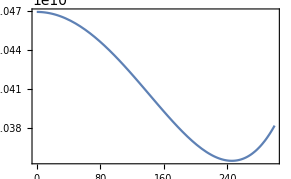

```mathematica
Plot[Vtree‵num/.{S->0},{h,0,300}]
```

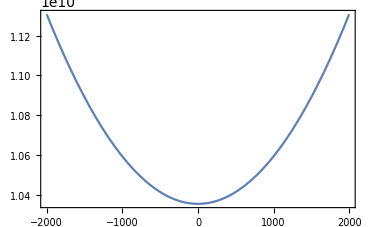

```mathematica
Plot[Vtree‵num/.{h->246},{S,-2000,2000}]
```

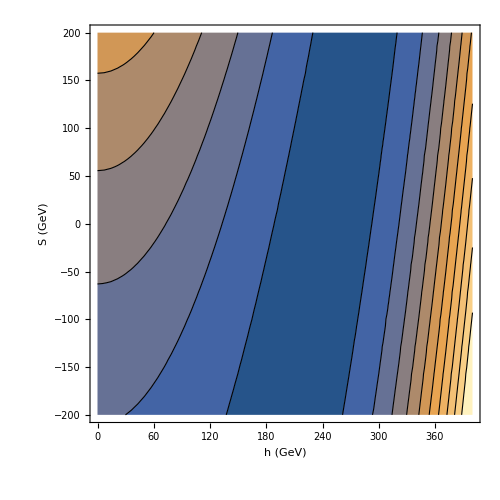

```mathematica
ContourPlot[Vtree‵num,{h,0,400},{S,-200,200},Contours->10,BaseStyle->{FontSize->20,FontFamily->"Times"},Frame->True,BoundaryStyle->None,FrameLabel->{Style["h (GeV)",FontFamily->"Times",FontSize->20],Style["S (GeV)",FontFamily->"Times",FontSize->20]},LabelStyle->{Black},FrameTicksStyle->Directive[FontFamily->"Times",FontSize->20],ImageSize->500]//CleanRegionPlot
```

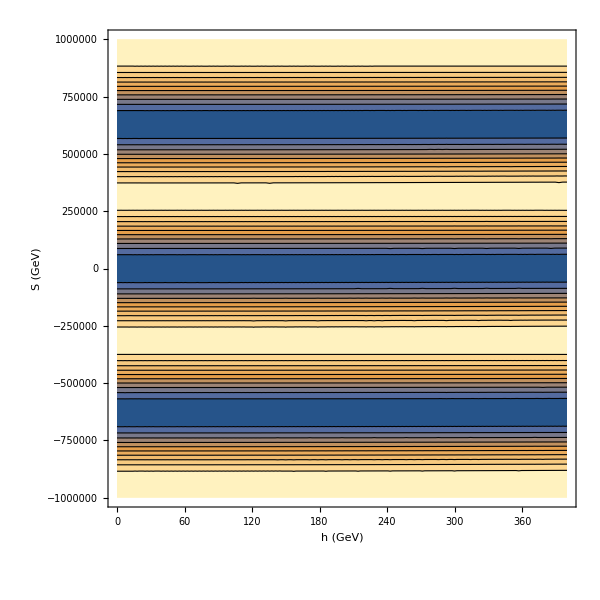

```mathematica
ContourPlot[Vtree‵num,{h,0,400},{S,-10^6,10^6},Contours->10,BaseStyle->{FontSize->20,FontFamily->"Times"},Frame->True,BoundaryStyle->None,FrameLabel->{Style["h (GeV)",FontFamily->"Times",FontSize->20],Style["S (GeV)",FontFamily->"Times",FontSize->20]},LabelStyle->{Black},FrameTicksStyle->Directive[FontFamily->"Times",FontSize->20],ImageSize->600]//CleanRegionPlot
```

Larger S value won’t have new physics information since it’s periodic and equivalent to each other.

## 1-loop level physics

### SM MSbar parameters

```mathematica
(*Parameter input and integral definition*)
mW=80.379;
mZ=91.1876;
mt=172.69;
αsmZ=0.1184;
g3mZ=√(4π αsmZ);
GF=1.1663787×10^-5;
vnum=(√2 GF)^(-1/2);
mhpole=125.13;
(*Define integrals. The scale is fixed to be mZ*)
A0[M_]:=M^2(1-Log[M^2/mZ^2]);
B0[p_,M1_,M2_]:=-NIntegrate[Log[(x M1^2+(1-x)M2^2-x(1-x)p^2)/mZ^2],{x,0,1}]
ytmZ=2(GF/(√2)mt^2)^(1/2)+mt/(√2 vnum^3(4π)^2)(-(mhpole^2-4 mt^2)B0[mt,mhpole,mt]+(mt^2(80 mW^2 mZ^2-64 mW^4-7 mZ^4)+40 mW^2 mZ^4-32 mW^4 mZ^2-17 mZ^6)/(9 mt^2 mZ^2)B0[mt,mt,mZ]+(mt^2 mW^2+mt^4-2 mW^4)/mt^2 B0[mt,0,mW]+((3 mhpole^2)/(mhpole^2-mW^2)+2 mW^2/mt^2+3 mW^2/(mW^2-mZ^2)-10)A0[mW]+(3 mW^2/(mW^2-mhpole^2)+1)A0[mhpole]+(36 mt^2 mZ^2-56 mW^2 mZ^2+64 mW^4-17 mZ^4)/(9 mt^2 mZ^2)A0[mt]+((3 mW^2)/(mZ^2-mW^2)+(32 mW^4-40 mW^2 mZ^2+17 mZ^4)/(9 mt^2 mZ^2)-3)A0[mZ]+mhpole^2/2-3 mt^2-9 mW^2+7 mZ^2/18+64 mW^4/(9 mZ^2))+mt/(√2 vnum (4π))αsmZ(-8 A0[mt]/mt^2-8/3)//Re;
g2mZ=2(√2 GF)^(1/2)mW+2 mW/((4π)^2 vnum^3)((mhpole^4/(6 mW^2)-2 mhpole^2/3+2 mW^2)B0[mW,mhpole,mW]+(-mt^4/mW^2-mt^2+2 mW^2)B0[mW,0,mt]+1/6(-48 mW^4/mZ^2+mZ^4/mW^2-68 mW^2+16 mZ^2)B0[mW,mW,mZ]+1/6(mhpole^2(9/(mhpole^2-mW^2)+1/mW^2)+mZ^2/mW^2+mW^2(9/(mW^2-mZ^2)+48/mZ^2)-27)A0[mW]+(2-(mhpole^2(mhpole^2+8 mW^2))/(6 mW^2(mhpole^2-mW^2)))A0[mhpole]+(mt^2/mW^2+1)A0[mt]+1/6(24 mW^2/mZ^2-mZ^2/mW^2+9 mW^2/(mZ^2-mW^2)-17)A0[mW]+1/36(-3 mhpole^2+18 mt^2+288 mW^4/mZ^2-374 mW^2-3 mZ^2))//Re;
g1mZ=2(√2 GF)^(1/2)√(mZ^2-mW^2)+(2 √(mZ^2-mW^2))/((4π)^2 vnum^3)((88/9-(124 mW^2)/(9 mZ^2)+(mhpole^2+34 mW^2)/(6(mZ^2-mW^2)))A0[mZ]+(mhpole^2-4 mW^2)/(2(mhpole^2-mW^2))A0[mhpole]+(-7/9-mt^2/(mZ^2-mW^2)+64 mW^2/(9 mZ^2))A0[mt]+(mhpole^4+2 mW^2(mW^2-15 mZ^2)+3 mhpole^2(2 mW^2+7 mZ^2))/(6(mhpole^2-mW^2)(mW^2-mZ^2))A0[mW]-(mt^4+mW^2 mt^2-2 mW^4)/(mW^2-mZ^2)B0[mW,0,mt]-(mhpole^4-4 mZ^2 mhpole^2+12 mZ^4)/(6(mW^2-mZ^2))B0[mZ,mhpole,mZ]+(mhpole^4-4 mW^2 mhpole^2+12 mW^4)/(6(mW^2-mZ^2))B0[mW,mhpole,mW]+(mZ^6-48 mW^6-68 mZ^2 mW^4+16 mZ^4 mW^2)/(6 mZ^2(mW^2-mZ^2))B0[mW,mW,mZ]+1/9(-23 mW^2+7 mt^2+17 mZ^2-(64 mt^2 mW^2)/mZ^2-(9 mW^2(mt^2-mW^2))/(mZ^2-mW^2))B0[mZ,mt,mt]+(mZ^6-48 mW^6-68 mZ^2 mW^4+16 mZ^4 mW^2)/(6 mZ^2(mZ^2-mW^2))B0[mZ,mW,mW]+1/36(576 mW^4/mZ^2-242 mW^2-3 mhpole^2+257 mZ^2+36 mW^2/(mZ^2-mW^2)+mt^2(82-256 mW^2/mZ^2)))//Re;
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.216781}. NIntegrate obtained -1.24537+2.46099 ⅈ and 0.000286423 for the integral and error estimates.

```mathematica
g1mZ
g2mZ
g3mZ
ytmZ
```

0.357394

0.651016

1.21978

0.977773

### 1-loop potential without scalar contribution

```mathematica
mWsq[h_]:=1/4 g2mZ^2 h^2;
mZsq[h_]:=1/4(g2mZ^2+g1mZ^2)h^2;
mtsq[h_]:=1/2 ytmZ^2 h^2;
VCW[h_]:=1/(64 π^2)(6 mWsq[h]^2(Log[mWsq[h]/mZ^2]-5/6)+3 mZsq[h]^2(Log[mZsq[h]/mZ^2]-5/6)-12 mtsq[h]^2(Log[mtsq[h]/mZ^2]-3/2));
V0Tpre[h_,S_]:=(Vtree‵nogs/.{v->vnum/(√2)}/.αvev)+VCW[h]
```

```mathematica
V0Tpre[h,S]//Simplify
```

A f (30312.1-0.5 h^2) sin(β+S/f)-1. f^2 μ_S^2 cos(S/f)+1. f^2 μ_S^2+0.25 h^4 λ+0.0465372 h^4-0.00828818 h^4 log(h)-0.5 h^2 μ_H^2

#### 1-loop parametrization

```mathematica
mass‵matrix‵1loop=D[V0Tpre[h,S]//Simplify,{{h,S},2}]/.{h->vnum,S->0}/.αvev;
der‵1loop=D[V0Tpre[h,S],{{h,S}}]/.{h->vnum,S->0}/.αvev;
P={{Cos[θ],Sin[θ]},{-Sin[θ],Cos[θ]}};
Diag‵mass={{mhpole^2,0},{0,mS^2}};
rotated=P.Diag‵mass.Inverse[P]//Simplify;
```

```mathematica
mass‵matrix‵1loop
```

(-1. A f sin(β)+181872. λ-1. μ_H^2-2862.09 | -246.22 A cos(β)
-246.22 A cos(β) | (3.63798×10^-12 A sin(β))/f+1. μ_S^2)

```mathematica
der‵1loop
```

{1/4 (-984.879 A f sin(β)+5.97074×10^7 λ-984.879 μ_H^2)-69945.5,-3.63798×10^-12 A cos(β)}

#### Benchmark point: mS=5GeV, sinθ=0.17

```mathematica
benchmark={f->10^5,θ->ArcSin[0.17],β->π/10,mS->5};
mass‵matrix‵1loop‵num=mass‵matrix‵1loop/.benchmark;
rotated‵num=rotated/.benchmark;
der‵1loop‵num=der‵1loop/.benchmark;
```

```mathematica
der‵1loop‵num
```

{1/4 (-3.04344×10^7 A+5.97074×10^7 λ-984.879 μ_H^2)-69945.5,-3.45992×10^-12 A}

```mathematica
sol‵1loop=NSolve[{rotated‵num[[1,1]]==mass‵matrix‵1loop‵num[[1,1]],rotated‵num[[1,2]]==mass‵matrix‵1loop‵num[[1,2]],rotated‵num[[2,2]]==mass‵matrix‵1loop‵num[[2,2]],der‵1loop‵num[[1]]==0},{λ,A,μHsq,μSsq}][[1]]
```

{λ→0.146672,A→11.1836,μ_H^2→-336984.,μ_S^2→476.78}

```mathematica
V0T[h_,S_]=V0Tpre[h,S]/.benchmark/.αvev/.sol‵1loop//Simplify
```

0.0832052 h^4-0.00828818 h^4 log(h)+(3.38997×10^10-559179. h^2) sin(S/100000+π/10)+168492. h^2-4.7678×10^12 cos(S/100000)+4.7678×10^12

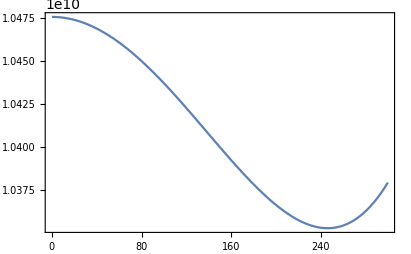

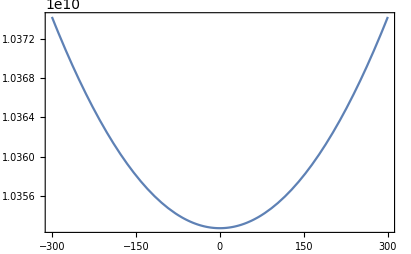

```mathematica
Plot[V0T[h,0],{h,0,300}]
Plot[V0T[vnum,S],{S,-300,300}]
```

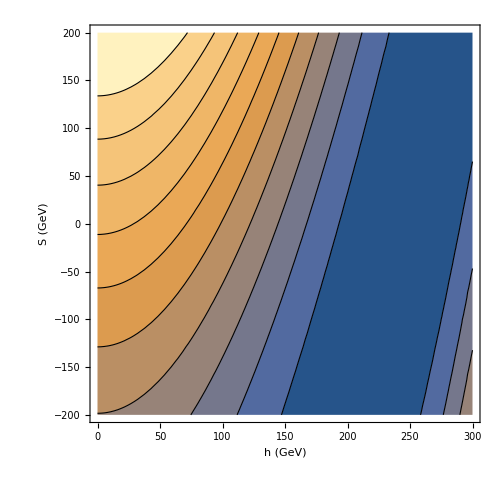

```mathematica
ContourPlot[V0T[h,S],{h,0,300},{S,-200,200},Contours->10,BaseStyle->{FontSize->20,FontFamily->"Times"},Frame->True,BoundaryStyle->None,FrameLabel->{Style["h (GeV)",FontFamily->"Times",FontSize->20],Style["S (GeV)",FontFamily->"Times",FontSize->20]},LabelStyle->{Black},FrameTicksStyle->Directive[FontFamily->"Times",FontSize->20],ImageSize->500]//CleanRegionPlot
```

1.04694×10^10

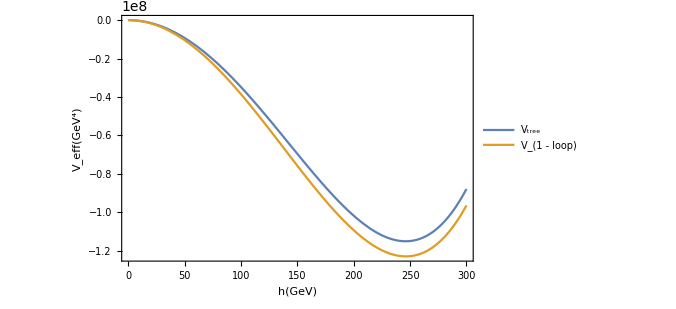

```mathematica
Vtree‵num‵vac=Vtree‵num/.{S->0,h->10^-5}
Plot[{(Vtree‵num/.{S->0})-Vtree‵num‵vac,(V0T[h,0]-V0T[10^-5,0])},{h,0,300},BaseStyle->{FontSize->20,FontFamily->"Times"},Frame->True,FrameLabel->{Style["h(GeV)",FontFamily->"Times",FontSize->20],Style["V_eff(GeV^4)",FontFamily->"Times",FontSize->20]},LabelStyle->{Black},FrameTicksStyle->Directive[FontFamily->"Times",FontSize->20],ImageSize->500,PlotLegends->Placed[{Style["V_tree",FontFamily->"Times",FontSize->22],Style["V_(1 - loop)",FontFamily->"Times",FontSize->22]},Scaled[{0.82,0.75}]]]
```

#### Scan over parameter space

```mathematica
headers={"mS","sin","lh","A","muHsq","muSsq"};
```

```mathematica
msbar‵forder5‵βπ10=Prepend[Flatten[Table[
{benchmark={f->10^5,θ->ArcSin[sinθ],β->π/10,mS->mSscan};
mass‵matrix‵1loop‵num=mass‵matrix‵1loop/.benchmark;
rotated‵num=rotated/.benchmark;
der‵1loop‵num=der‵1loop/.benchmark;
sol‵1loop=NSolve[{rotated‵num[[1,1]]==mass‵matrix‵1loop‵num[[1,1]],rotated‵num[[1,2]]==mass‵matrix‵1loop‵num[[1,2]],rotated‵num[[2,2]]==mass‵matrix‵1loop‵num[[2,2]],der‵1loop‵num[[1]]==0},{λ,A,μHsq,μSsq}][[1]];
mSscan,
sinθ,
λmsbar=λ/.sol‵1loop,
Amsbar=A/.sol‵1loop,
μhsqmsbar=μHsq/.sol‵1loop,
μSsqmsbar=μSsq/.sol‵1loop
},
{mSscan,1,15,1},{sinθ,0.02,0.3,0.02}],1],headers];
```

```mathematica
Export[NotebookDirectory[]<>"output/f_5_beta_pi10.csv",msbar‵forder5‵βπ10]
```

/Users/quarkquartet/Library/CloudStorage/Dropbox/Research_Project/2022-1-SFOPT_light_singlet/02-Analysis/model_setup/output/f_5_beta_pi10.csv

### With scalar correction in the potential

#### Potential

```mathematica
mWsq[h_]:=1/4 g2mZ^2 h^2;
mZsq[h_]:=1/4(g2mZ^2+g1mZ^2)h^2;
mtsq[h_]:=1/2 ytmZ^2 h^2;
VCW[h_,S_]:=1/(64 π^2)(6 mWsq[h]^2(Log[mWsq[h]/mZ^2]-5/6)+3 mZsq[h]^2(Log[mZsq[h]/mZ^2]-5/6)-12 mtsq[h]^2(Log[mtsq[h]/mZ^2]-3/2)+3 mgs^2(Log[mgs/mZ^2]-3/2)+mhtree^2(Log[mhtree/mZ^2]-3/2)+mStree^2(Log[mStree/mZ^2]-3/2));
V0Tpre[h_,S_]:=(Vtree‵nogs+VCW[h,S]/.{v->vnum/(√2)}/.αvev)
```

#### Parametrization

```mathematica
mass‵matrix‵1loop=D[V0Tpre[h,S]//Simplify,{{h,S},2}]/.{h->vnum,S->0}/.αvev;
der‵1loop=D[V0Tpre[h,S],{{h,S}}]/.{h->vnum,S->0}/.αvev;
P={{Cos[θ],Sin[θ]},{-Sin[θ],Cos[θ]}};
Diag‵mass={{mhpole^2,0},{0,mS^2}};
rotated=P.Diag‵mass.Inverse[P]//Simplify;
```

#### Benchmark

```mathematica
benchmark={f->10^5,θ->ArcSin[0.17],β->π/10,mS->5};
mass‵matrix‵1loop‵num=mass‵matrix‵1loop/.benchmark//N//Simplify;
rotated‵num=rotated/.benchmark//N//Simplify;
der‵1loop‵num=der‵1loop/.benchmark//N//Simplify;
```

```mathematica
eqns={rotated‵num[[1,1]]==mass‵matrix‵1loop‵num[[1,1]],rotated‵num[[1,2]]==mass‵matrix‵1loop‵num[[1,2]],rotated‵num[[2,2]]==mass‵matrix‵1loop‵num[[2,2]],der‵1loop‵num[[1]]==0};
```

```mathematica
sol‵1loop=FindRoot[eqns,{{λ,0.14},{A,11.},{μHsq,-330000},{μSsq,476}}]
```

{λ→0.14707+4.67006×10^-28 ⅈ,A→11.264+1.83773×10^-26 ⅈ,μ_H^2→-339459.-5.55865×10^-22 ⅈ,μ_S^2→480.134+8.14256×10^-25 ⅈ}

```mathematica
V0T[h_,S_]=V0Tpre[h,S]/.benchmark/.αvev/.sol‵1loop//Re//Simplify;
```

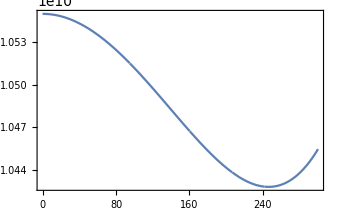

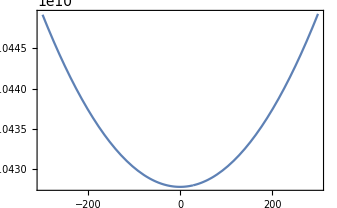

```mathematica
Plot[V0T[h,0],{h,0,300}]
Plot[V0T[vnum,S],{S,-300,300}]
```

#### Scan over the parameter space

```mathematica
headers={"mS","sin","lh","A","muHsq","muSsq"};
```

```mathematica
msbar‵forder5‵βπ10=Prepend[Flatten[Table[
{benchmark={f->10^5,θ->ArcSin[sinθ],β->π/10,mS->mSscan,mh->mhpole,v->vnum};
mass‵matrix‵1loop‵num=mass‵matrix‵1loop/.benchmark;
rotated‵num=rotated/.benchmark;
der‵1loop‵num=der‵1loop/.benchmark;
{Atree,μStree,λtree}={A,μSsq,λ}/.sol‵tree/.benchmark;
μHtree=μHsq/.μHsol/.sol‵tree/.benchmark;
sol‵1loop=FindRoot[{rotated‵num[[1,1]]==mass‵matrix‵1loop‵num[[1,1]],rotated‵num[[1,2]]==mass‵matrix‵1loop‵num[[1,2]],rotated‵num[[2,2]]==mass‵matrix‵1loop‵num[[2,2]],der‵1loop‵num[[1]]==0},{{λ,λtree},{A,Atree},{μHsq,μHtree},{μSsq,μStree}}];
mSscan,
sinθ,
λmsbar=λ/.sol‵1loop//Re,
Amsbar=A/.sol‵1loop//Re,
μhsqmsbar=μHsq/.sol‵1loop//Re,
μSsqmsbar=μSsq/.sol‵1loop//Re
},
{mSscan,1,15,1},{sinθ,0.02,0.3,0.02}],1],headers];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
Export[NotebookDirectory[]<>"output/f_5_beta_pi10.csv",msbar‵forder5‵βπ10];
```